```mathematica
plotContour[mu1__, mu2__,sigma__,aLabel_]:=Show[ContourPlot[PDF[MultinormalDistribution[{0,0},IdentityMatrix[2]],{x,y}],{x,-3,11},{y,-3,11},ContourShading->None,Contours->Function[{min,max},Range[min,max,0.01]],ContourStyle->Directive[Black,Thick],PlotRange->Full,FrameTicks->None,PlotLabel->aLabel,LabelStyle->Directive["Subtitle",Black],PlotPoints->100],
ContourPlot[PDF[MultinormalDistribution[mu1,DiagonalMatrix[sigma]],{x,y}],{x,-3,11},{y,-3,11},ContourShading->None,Contours->Function[{min,max},Range[min,max,0.01]],ContourStyle->Directive[Blue,Dashed,Thick],PlotRange->Full,PlotPoints->100],ContourPlot[PDF[MultinormalDistribution[{8,8},IdentityMatrix[2]],{x,y}],{x,-3,11},{y,-3,11},ContourShading->None,Contours->Function[{min,max},Range[min,max,0.01]],ContourStyle->Directive[Black,Thick],PlotRange->Full,PlotPoints->100],ContourPlot[PDF[MultinormalDistribution[mu2,DiagonalMatrix[sigma]],{x,y}],{x,-3,11},{y,-3,11},ContourShading->None,Contours->Function[{min,max},Range[min,max,0.01]],ContourStyle->Directive[Orange,Dashed,Thick],Contours->50,PlotRange->Full,PlotPoints->100],ImageSize->300]
```

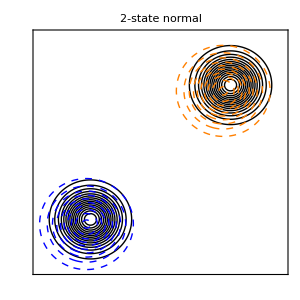

```mathematica
g1=plotContour[{-0.2256035,-0.2759647},{7.5813273, 7.6541182},{1.541746, 1.581182},"2-state normal"]
```

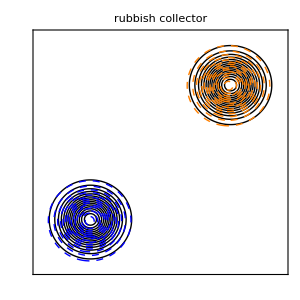

```mathematica
g3=plotContour[{-0.04429909,-0.08280655},{7.88259312, 7.96074249},{1.015293, 1.038413},"rubbish collector"]
```

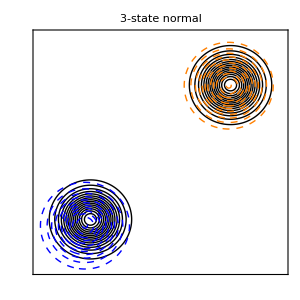

```mathematica
g2=plotContour[{-0.3135811,-0.372200},{7.8946867, 7.964446},{1.295070, 1.335942},"3-state normal"]
```

```mathematica
gfinal=Grid[{{g1,g2},{g3,}}]
```

-Graphics- | -Graphics-
-Graphics- |

```mathematica
Export["../figures/state_cleanliness.pdf",gfinal]
```

../figures/state_cleanliness.pdf